# Assemble sparse matrices from the matrix elements

Two different types of matrices are assembled:
1. The full matrix, all l,m included. This is used for time-dependent solutions.
2. The augmented matrix, only even l,m (due to symmetries in the Jeffery equations), and the l=0 mode removed and moved to the right hand side, such that the matrix equation is actually invertible.

NOTE: The optimizations in here are true not in general.
Even l,m : Due to symmetries in the Jeffery problem in shear flow
Conjugate matrixelementns upon Δm->-Δm because P is real-valued

## Matrix elements (taken from previous notebook)

These are the matrix elements from the previous file, just copied and pasted.

```mathematica
matrixelements={{{-2,0},Piecewise[{{0, l<2||((l≥2+m||l+m≤1)&&m≥0)||(m<0&&l+m≥2)}, {1/2 ⅈ (-1+l) m √(((-1+l-m) (l-m) (-1+l+m) (l+m))/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))), l>1+m&&l+m>1}, {(ⅈ (-2+l-m) √(((-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))))/(-4+8 l), l≥2&&l+m>1}, {((-2+l+m) √(-((-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))))/(-4+8 l), True}}]},{{-2,2},Piecewise[{{(ⅈ (-2+l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m))/((-3+2 l) (1+2 l))) Λ)/(-4+8 l), l≥2&&(l≥4+m||m<-2)}, {1/4 ⅈ (-1+l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m) (l+m)^2)/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))) Λ, l>3+m}, {0, True}}]},{{0,0},Piecewise[{{-invPe l (1+l)+(ⅈ m)/3, l<1}, {-invPe l (1+l)+(ⅈ m)/2, True}}]},{{0,2},Piecewise[{{3/4 ⅈ (1+l) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(-3+l (1+4 l (2+l)))^2) Λ, l≥1&&(l≥2+m||m<-2)}, {-1/4 ⅈ (1+l) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(-3+l (1+4 l (2+l)))^2) (1+2 m) Λ, l>1+m}, {0, True}}]},{{2,2},-(ⅈ (3+l) √(((1+l+m) (2+l+m) (3+l+m) (4+l+m))/(5+12 l+4 l^2)) Λ)/(12+8 l)},{{-2,-2},Conjugate[Piecewise[{{(ⅈ (-2+l) √(((-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))) Λ)/(-4+8 l), l≥2&&(l+m≥4||m>2)}, {1/4 ⅈ (-1+l) √(((l-m)^2 (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))) Λ, l+m>3}, {0, True}}]]},{{0,-2},Conjugate[Piecewise[{{3/4 ⅈ (1+l) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(-3+l (1+4 l (2+l)))^2) Λ, l≥1&&(l+m≥2||m>2)}, {1/4 ⅈ (1+l) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(-3+l (1+4 l (2+l)))^2) (-1+2 m) Λ, l+m>1}, {0, True}}]]},{{2,-2},(ⅈ (3+l) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m))/(5+12 l+4 l^2)) Λ)/(12+8 l)}}
```

{{{-2,0},Piecewise[{{0, l<2||((l≥2+m||l+m≤1)&&m≥0)||(m<0&&l+m≥2)}, {1/2 ⅈ (-1+l) m √(((-1+l-m) (l-m) (-1+l+m) (l+m))/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))), l>1+m&&l+m>1}, {(ⅈ (-2+l-m) √(((-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))))/(-4+8 l), l≥2&&l+m>1}, {((-2+l+m) √(-((-1+l-m) (l-m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))))/(-4+8 l), True}}]},{{-2,2},Piecewise[{{(ⅈ (-2+l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m))/((-3+2 l) (1+2 l))) Λ)/(-4+8 l), l≥2&&(l≥4+m||m<-2)}, {1/4 ⅈ (-1+l) √(((-3+l-m) (-2+l-m) (-1+l-m) (l-m) (l+m)^2)/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))) Λ, l>3+m}, {0, True}}]},{{0,0},Piecewise[{{-invPe l (1+l)+(ⅈ m)/3, l<1}, {-invPe l (1+l)+(ⅈ m)/2, True}}]},{{0,2},Piecewise[{{3/4 ⅈ (1+l) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(-3+l (1+4 l (2+l)))^2) Λ, l≥1&&(l≥2+m||m<-2)}, {-1/4 ⅈ (1+l) √(((-1+l-m) (l-m) (1+l+m) (2+l+m))/(-3+l (1+4 l (2+l)))^2) (1+2 m) Λ, l>1+m}, {0, True}}]},{{2,2},-(ⅈ (3+l) √(((1+l+m) (2+l+m) (3+l+m) (4+l+m))/(5+12 l+4 l^2)) Λ)/(12+8 l)},{{-2,-2},Conjugate[Piecewise[{{(ⅈ (-2+l) √(((-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((-3+2 l) (1+2 l))) Λ)/(-4+8 l), l≥2&&(l+m≥4||m>2)}, {1/4 ⅈ (-1+l) √(((l-m)^2 (-3+l+m) (-2+l+m) (-1+l+m) (l+m))/((1-2 l)^2 (-1+l)^2 (-3+2 l) (1+2 l))) Λ, l+m>3}, {0, True}}]]},{{0,-2},Conjugate[Piecewise[{{3/4 ⅈ (1+l) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(-3+l (1+4 l (2+l)))^2) Λ, l≥1&&(l+m≥2||m>2)}, {1/4 ⅈ (1+l) √(((1+l-m) (2+l-m) (-1+l+m) (l+m))/(-3+l (1+4 l (2+l)))^2) (-1+2 m) Λ, l+m>1}, {0, True}}]]},{{2,-2},(ⅈ (3+l) √(((1+l-m) (2+l-m) (3+l-m) (4+l-m))/(5+12 l+4 l^2)) Λ)/(12+8 l)}}

## Complete matrix, all modes

```mathematica
assemblesparse[maxl_]:=Module[{row,p,q,col,dl,dm,l2,m2,sparserules,value,size,k,delta},
size = Sum[2 l+1,{l,0,maxl}];
Print[size];
row=1;
sparserules={};
For[p=0,p<=maxl,p++,
For[q=-p,q≤p,q++,
For[k=1,k≤Length[matrixelements],k++,
delta=matrixelements[[k,1]];
dl=delta[[1]];
dm=delta[[2]];
l2=p-dl;
m2 = q-dm;
If [l2≥0 && l2≤maxl&&Abs[m2]≤l2,
col = 1+l2(l2+1)+m2;
value=Simplify[ matrixelements[[k,2]]/.{l->l2,m->m2},{{Λ,stEff,l,m,invPe}∈Reals}];
If[Not[value===0],AppendTo[sparserules,{row,col}->value]];
];
]
row++;
]
];
SparseArray[sparserules]
];
```

## Test it

25

32136

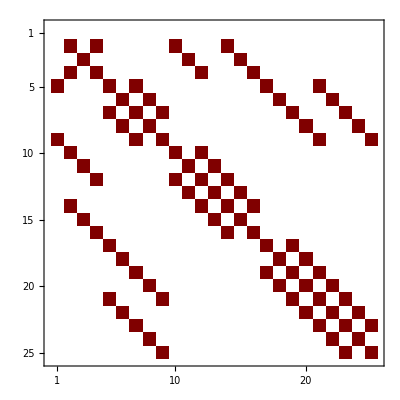

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/2-2 invPe | 0 | -(3 ⅈ Λ)/10 | 0 | 0 | 0 | 0 | 0 | ⅈ √(3/70) Λ | 0 | 0 | 0 | -(ⅈ Λ)/(5 √14) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 invPe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/(√70) | 0 | 0 | 0 | -(ⅈ Λ)/(√70) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (3 ⅈ Λ)/10 | 0 | ⅈ/2-2 invPe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/(5 √14) | 0 | 0 | 0 | -ⅈ √(3/70) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ √(3/10) Λ | 0 | 0 | 0 | -ⅈ-6 invPe | 0 | -1/7 ⅈ √(3/2) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 ⅈ Λ)/(√21) | 0 | 0 | 0 | -1/7 ⅈ √(2/15) Λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/2-6 invPe | 0 | -(3 ⅈ Λ)/14 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ √(2/21) Λ | 0 | 0 | 0 | -1/7 ⅈ √(2/3) Λ | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/7 ⅈ √(3/2) Λ | 0 | -6 invPe | 0 | -1/7 ⅈ √(3/2) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/7 ⅈ √2 Λ | 0 | 0 | 0 | -1/7 ⅈ √2 Λ | 0 | 0
0 | 0 | 0 | 0 | 0 | (3 ⅈ Λ)/14 | 0 | ⅈ/2-6 invPe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/7 ⅈ √(2/3) Λ | 0 | 0 | 0 | -ⅈ √(2/21) Λ | 0
-ⅈ √(3/10) Λ | 0 | 0 | 0 | 0 | 0 | 1/7 ⅈ √(3/2) Λ | 0 | ⅈ-6 invPe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/7 ⅈ √(2/15) Λ | 0 | 0 | 0 | -(2 ⅈ Λ)/(√21)
0 | 2 ⅈ √(6/35) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/2 (ⅈ+8 invPe) | 0 | -(ⅈ Λ)/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ √(2/35) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ-12 invPe | 0 | -(ⅈ Λ)/(√30) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2/5 ⅈ √(2/7) Λ | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/(2 √15) | 0 | -ⅈ/2-12 invPe | 0 | -(ⅈ Λ)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/(√30) | 0 | -12 invPe | 0 | -(ⅈ Λ)/(√30) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2/5 ⅈ √(2/7) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/5 | 0 | ⅈ/2-12 invPe | 0 | -(ⅈ Λ)/(2 √15) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ √(2/35) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/(√30) | 0 | ⅈ-12 invPe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ √(6/35) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ Λ)/(2 √15) | 0 | (3 ⅈ)/2-12 invPe | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (5 ⅈ Λ)/(√21) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ-20 invPe | 0 | -(3 ⅈ Λ)/(11 √7) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (5 ⅈ Λ)/(√42) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 ⅈ)/2-20 invPe | 0 | -(9 ⅈ Λ)/(22 √7) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (5 ⅈ Λ)/(7 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ Λ)/(11 √7) | 0 | -ⅈ-20 invPe | 0 | -9/77 ⅈ √(5/2) Λ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (5 ⅈ Λ)/(7 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (9 ⅈ Λ)/(22 √7) | 0 | -ⅈ/2-20 invPe | 0 | -(15 ⅈ Λ)/77 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/7 ⅈ √(5/6) Λ | 0 | 0 | 0 | 1/7 ⅈ √(5/6) Λ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/77 ⅈ √(5/2) Λ | 0 | -20 invPe | 0 | -9/77 ⅈ √(5/2) Λ | 0 | 0
0 | 0 | 0 | 0 | 0 | -(5 ⅈ Λ)/(7 √6) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (15 ⅈ Λ)/77 | 0 | ⅈ/2-20 invPe | 0 | -(9 ⅈ Λ)/(22 √7) | 0
0 | 0 | 0 | 0 | 0 | 0 | -(5 ⅈ Λ)/(7 √2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9/77 ⅈ √(5/2) Λ | 0 | ⅈ-20 invPe | 0 | -(3 ⅈ Λ)/(11 √7)
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 ⅈ Λ)/(√42) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (9 ⅈ Λ)/(22 √7) | 0 | (3 ⅈ)/2-20 invPe | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 ⅈ Λ)/(√21) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 ⅈ Λ)/(11 √7) | 0 | 2 ⅈ-20 invPe)

```mathematica
maxl=4;
sparsetest = assemblesparse[maxl];
ByteCount[sparsetest]
MatrixPlot[sparsetest]
MatrixForm[sparsetest]
```

## Augmented matrix, even l,m

Here we’ll save the real and imaginary parts of c_lm as separate elements, so if we want to we can export from mathematica and use any sparse solver we like.

sparseindex[l,m] gives the index of the real part of c_lm, the imaginary is the next index

```mathematica
sparseindex[l_Integer,m_Integer]:=m+(l/2)^2-(-1+m) KroneckerDelta[0,m]/;EvenQ[l]&&EvenQ[m];
(* Computed from: sparseindex[l_,m_]:= 1 + Sum[1+k,{k,0,l-2,2}]+(1-KroneckerDelta[m,0])(m-1); *)
```

These are the functions that do the actual assembling.

```mathematica
AppendRules[list_,pos_->val_]:=Module[{},
existingpos=Position[list,pos->_];
If[Length[existingpos]==0,
Append[list,pos->val],

existingpos=existingpos[[1,1]];
existingrule = list[[existingpos]];
newrule = existingrule /.(pos->x_):>(pos->x+val);
ReplacePart[list,existingpos->newrule]
]
];
assemblesparseoptimised[maxl_]:=Module[{row,p,q,col,dl,dm,l2,m2,sparserules,value,size,k,delta,temprules,m2sign,m2magn,recol,imcol,revalue,imvalue},
size =sparseindex[maxl,maxl]+1;
Print[size];
row=1;
sparserules={};
For[p=0,p<=maxl,p+=2,
For[q=0,q≤p,q+=2,
temprules = {};
For[k=1,k≤Length[matrixelements],k++,
delta=matrixelements[[k,1]];
dl=delta[[1]];
dm=delta[[2]];
l2=p-dl;
m2 = q-dm;
m2sign = Sign[m2];
m2magn=Abs[m2];
If [l2≥0 && l2≤maxl&&Abs[m2]≤l2,
recol = sparseindex[l2,m2magn];
imcol = recol+1;
value=Simplify[ matrixelements[[k,2]]/.{l->l2,m->m2}];
revalue=Simplify[Re[value],{Λ∈Reals,invPe∈Reals,stEff∈Reals}];
imvalue=Simplify[Im[value],{Λ∈Reals,invPe∈Reals,stEff∈Reals}];
(*Row for real value*)

If[Not[revalue===0],
temprules=AppendRules[temprules,{row,recol}->revalue];
];
If[Not[imvalue===0]&&Not[m2==0],
temprules=AppendRules[temprules,{row,imcol}->-imvalue m2sign];
];
(*Row for imaginory value*)
If[Not[q==0],
If[Not[revalue===0]&&Not[m2==0],
temprules=AppendRules[temprules,{row+1,imcol}->revalue m2sign];
];
If[Not[imvalue===0],
temprules=AppendRules[temprules,{row+1,recol}->imvalue];
];
];

];
];
sparserules = Join[sparserules,temprules];
row+=If[q==0,1,2];
];
PrintTemporary[p]
];

SparseArray[sparserules]
]/;EvenQ[maxl];
```

## Test it

49

78152

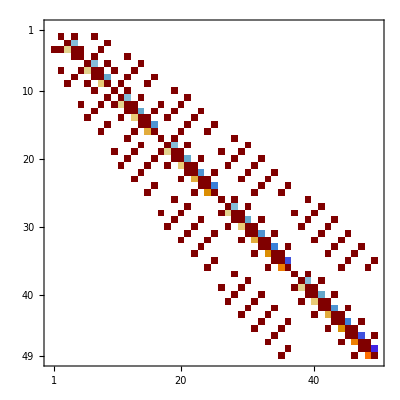

```mathematica
maxl=12;
sparsetest = assemblesparseoptimised[maxl];
ByteCount[sparsetest]
MatrixPlot[sparsetest]
(*MatrixForm[sparsetest]*)
```

## Assemble up to some size, and save it to a .mx file (platform specific, dont transfer .mx around)

```mathematica
maxl = 20;
sparseOptimised=assemblesparseoptimised[maxl]
sparseAugmented = sparseOptimised[[2;;,2;;]];
augmentedB=-sparseOptimised[[2;;,1]] * 1/(2 Sqrt[Pi])//Normal;
DumpSave[ToString[StringForm["augmentedMatrix_lmax``.mx",maxl]],{sparseAugmented,augmentedB}]
```

121

SparseArray[<791>,{121,121}]

{SparseArray[<790>,{120,120}],{0,0,1/2 √(3/(10 π)) Λ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## See if it works

{120,120}

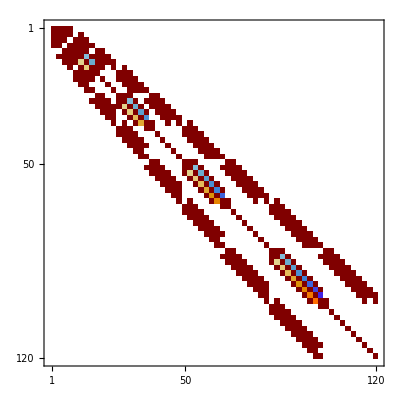

```mathematica
Clear[sparseAugmented,augmentedB]
Get[ToString[StringForm["augmentedMatrix_lmax``.mx",maxl]]]
Dimensions[sparseAugmented]
MatrixPlot[sparseAugmented]
```